# Eigenestados por el método de expansión

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"AdvancedMapping.wl"}]]
```

Frontera

```mathematica
cu = 0.5;
```

```mathematica
Manipulate[
RegionPlot[(x-1)^2+(y-1)^2<1&&x<1+cu,{x,0,2},{y,0,2}],
{{cu,0.5},-1,1}
]
```

Parámetros

```mathematica
M = 6;
```

Definición de la frontera y la base

```mathematica
FrII[x_,y_]:=If[(x-1)^2+(y-1)^2<1&&x<1+cu,0,1];
ϕm[x_,y_,m1_,m2_]:=Sin[(π m1 x)/2]Sin[(π m2 y)/2];
basisIndexes = Flatten[Table[{m1,m2},{m1,1,M},{m2,1,M}],1];
```

Cómputo de la ν

```mathematica
HND = ProgressParallelTable[
Quiet@NIntegrate[
ϕm[x,y,basisIndexes[[k1,1]],basisIndexes[[k1,2]]]*FrII[x,y]*ϕm[x,y,basisIndexes[[k2,1]],basisIndexes[[k2,2]]],
{x,0,2},{y,0,2},
AccuracyGoal->8,
Method->"MultidimensionalRule"
],
{k1,1,Length[basisIndexes]},{k2,1,Length[basisIndexes]}
];
```

```mathematica
MatrixPlot[HND,PlotLegends->Automatic]
```

-Graphics-

Considerando que m = 1 y ℏ = 1.

```mathematica
HD = DiagonalMatrix[Table[(0.5 π^2(basisIndexes[[k,1]]^2+basisIndexes[[k,2]]^2))/4,{k,1,Length[basisIndexes]}]];
```

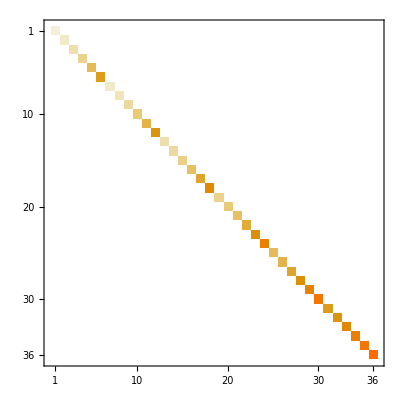

```mathematica
MatrixPlot[HD]
```

Vamos a considerar que V_0 = 200000.

```mathematica
HM = HD + 200000 HND;
NEV = Eigenvalues[HM];
EV = Sort[NEV];
Evec = Eigenvectors[HM][[Ordering[NEV]]];
```

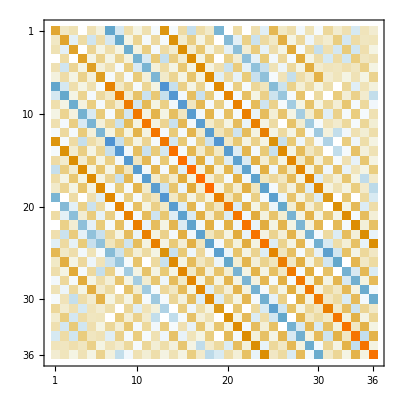

```mathematica
MatrixPlot[HM]
```

```mathematica
ϕSolution[x_,y_,nes_]:=Sum[Evec[[nes,k]]*ϕm[x,y,basisIndexes[[k,1]],basisIndexes[[k,2]]],{k,1,Length[basisIndexes]}];
```

```mathematica
Manipulate[
DensityPlot[
ϕSolution[x,y,nes]^2,{x,0,2},{y,0,2},
RegionFunction->Function[{x,y,z},(x-1)^2+(y-1)^2<1&&x<1+cu],
AxesOrigin->{1,1},
ColorFunction->"Rainbow",
Mesh->Automatic,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->350,
FrameLabel->{Style["x",15],Style["y",15]},
PlotLegends->Automatic,
PlotRange->{{0,2},{0,2},All},
PlotLabel->EV[[nes]]
],
{nes,1,Length[Evec],1}
]
```

- Cambiar la base para ver si obtenemos mejor precisión.
- Implementación de este mismo algoritmo en C++.
- Probar diferentes formas para el potencial.
- Normalizar.